# Задание 03.

## Одномерный квантовый осциллятор

## Мосейков Игнатий Геннадьевич № 21372

## Задача

Стационарное уравнение Шрёдингера в поле осциллятора имеет следующий вид:

[-(p̂)^2/(2m)+(m ω^2 x^2)/2]ψ_n=E_n ψ_n.

Далее будем работать в системе единиц ℏ = m = ω = 1.

Ваша задача заключается в нахождении волновых функций основного и возбужденных состояний ψ_n, n=0,1,2 ..

### Указания

1) Для поиска собственных функций ψ[n]  удобно ввести понижающий и повышающий операторы

(â)_-=(x+ⅈ p̂)/(√2), (â)_+=(x-ⅈ p̂)/(√2),

где оператор импульса в координатном представлении p̂=-ⅈ ⅆ/ⅆx. 
Определите действие понижающего и повышающего операторов: aminus, aplus

```mathematica
ℏ=m=ω=1;
p=-ⅈ D[#,x]&
aminus = (x #+ I p[#, x]) /Sqrt[2] &
aplus = (x #- I p[#, x]) /Sqrt[2]&
```

-ⅈ ∂_x #1&

(x #1+ⅈ p[#1,x])/(√2)&

(x #1-ⅈ p[#1,x])/(√2)&

2) Понижающий оператор, действуя на основное состояние ψ_0 должен давать 0:

(â)_-ψ_0=0

Это даст дифференциальное уравнение на неизвестную волновую функцию  ψ_0

```mathematica
equation1 = {aminus @ psi[x] == 0};
rule1 = DSolve[equation1, psi[x], x]// First
ψ0[k_] = psi[x]/.rule1
```

{psi[x]→ⅇ^(-x^2/2) C[1]}

ⅇ^(-x^2/2) C[1]

3) Решите дифференциальное уравнение (3)  для волновой функции ψ_0 и нормируйте ее так, чтобы

∫_(-∞)^(+∞) (|ψ_0|)^2 ⅆx=1.

```mathematica
sol1=Solve[Integrate[(Abs[ψ0[x]])^2,{x,-∞,+∞}]==1,C[1]]
ψ0norm[x_]=ψ0[x]/.sol1[[2]]
eq1=(aminus @ ψ0norm[x]==0)
```

{{C[1]→-1/π^(1/4)},{C[1]→1/π^(1/4)}}

(ⅇ^(-x^2/2))/π^(1/4)

True

4) n-ое возбужденное состояние, ψ_n, определяется рекурсивно с помощью повышающего оператора:

ψ_n=((â)_+ψ_(n-1))/(√n).

Воспользуйтесь конструкцией вида f[n_] := f[n] = ..., чтобы вычислять и сохранять результаты для ψ_n.

```mathematica
Clear[ψ]
ψ[x_, n_] := ψ[x, n] = aplus @ ψ[x, n -1] / Sqrt[n] //Factor
{ψ0[x], sol1[[2]]}
ψ[x_, 0] := Evaluate[ψ0[x]/.sol1[[2]]]
ψ[x, 3]
```

{ⅇ^(-x^2/2) C[1],{C[1]→1/π^(1/4)}}

(ⅇ^(-x^2/2) x (-3+2 x^2))/(√3 π^(1/4))

5) Распечатайте несколько первых волновых функций (должны получиться произведения экспоненты на полиномы Эрмита)

```mathematica
ψ[x,30]
```

(ⅇ^(-x^2/2) (-6190283353629375+185708500608881250 x^2-866639669508112500 x^4+1502175427147395000 x^6-1287578937554910000 x^8+629483036137956000 x^10-190752435193320000 x^12+37731250917360000 x^14-5030833455648000 x^16+460337701824000 x^18-29073960115200 x^20+1258612992000 x^22-36481536000 x^24+673505280 x^26-7127040 x^28+32768 x^30))/(15692092416000 √1077205 π^(1/4))

6) Проверьте нормировку ваших волновых функций:

∫_(-∞)^(+∞) (|ψ_n|)^2 ⅆx=1.

```mathematica
result = NIntegrate[ψ[x, 40] ^ 2, {x, -Infinity, Infinity}]
```

1.

7) Определить действие гамильтониана h через операторы aminus, aplus

ĥ=(a_+a_-+1/2)

```mathematica
Ham = aplus @ aminus @ # + # /2 &
```

aplus[aminus[#1]]+#1/2&

8) Проверьте, что гамильтониан, действуя на функции ψ_n, выдает правильные значения энергии.

```mathematica
Energy[n_] :=(Ham @ ψ[x, n]// Simplify) / ψ[x, n]
Energy[1]
Energy[10]
Energy[21]
Evaluate[ψ[0, 0] + Energy[2]]
```

3/2

21/2

43/2

5/2+1/π^(1/4)

9) Постройте графики волновых функций основного и нескольких первых возбужденных состояний. Для квадратов модулей волновых функций, сдвинутых по оси y на величину энергий этих состояний, должна получиться следующая картина:

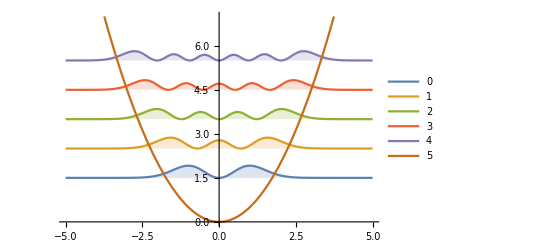

```mathematica
Plot[{Evaluate[Table[ψ[x, n]^2 + Energy[n], {n, 5}]], x^2 / 2}, {x, -5, 5}, PlotRange->{0, 7},   Filling->{Table[n->(Evaluate[Energy[n]]), {n,0,5}], None}, PlotLegends->{Table[n, {n, 0, 5}], "U = x^2/2"}]
```

10) Определите функцию matrixElement[f, n1, n2], которая бы вычисляла матричный элемент для оператора физической величины
f̂ между состояниями с номерами n_1, n_2. Оператор f мы будем передавать в виде чистой функции (Function). Проверьте работу (например, на операторах энергии, импульса, координаты)

```mathematica
MatrixElement[op_, i_, j_]:= Integrate[ψ[x, i] op @ ψ[x, j], {x, -Infinity, Infinity}] // Simplify
opX = x # &;
MatrixElement[p, 4, 5]
```

-ⅈ √(5/2)

```mathematica
MatrixElement[opX, 1,1]
```

0

```mathematica
MatrixElement[aplus, 1, 0]
```

1

```mathematica
MatrixElement[aminus, 1, 2]
```

√2

```mathematica
MatrixElement[Ham, 3,3]
```

7/2